## 165Lu

```mathematica
ClearAll["Global`*"]
```

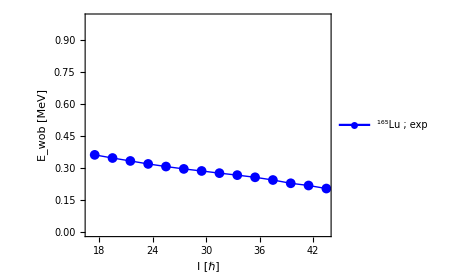

```mathematica
yrastEn=Sort[{15624,14384.9,13195.6,12062.1,10985.9,9966.5,9003.5,8094.7,7239.0,6435.7,5685.4,4988.6,4347.3,3765.2,3240.1,2794.1,2409.3}];
wob1En=Sort[{15209,14009.0,12858.0,11768.4,10733.3,9752.2,8825.6,7953.5,7133.6,6367.9,5656.5,5001.4,4403.4,3864.5}];
yrastSpin=Table[i/2,{i,25,89,4}];
wob1Spin=Table[i/2,{i,35,87,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+2]]+yrast[[i+3]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","165"],"Lu ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/165Lu.pdf",fig];
Show[fig]
```